# Dynamical Systems Analysis of Ellis and Maartens’ Emergent Universe

## Dimensionless Variables - 3D

```mathematica
deu:=u'=-u^2-(1/3)*(ψ^2-v)
deψ:=ψ'=-3*u*ψ-2*Sqrt[v]*(1-Sqrt[v])
dev:=v'=-2*ψ*Sqrt[v]*(1-Sqrt[v])
```

```mathematica
(*Solve the system of equations for the fixed points*)
FPs=Solve[{deu==0,deψ==0,dev==0},{u,ψ,v}]
```

{{u→0,ψ→0,v→0},{u→0,ψ→0,v→0},{u→-1/(√3),ψ→0,v→1},{u→1/(√3),ψ→0,v→1},{u→0,ψ→-1,v→1},{u→-1/(√3),ψ→0,v→1},{u→1/(√3),ψ→0,v→1},{u→0,ψ→1,v→1}}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={u/.FPs[[1,1]],ψ/.FPs[[1,2]],v/.FPs[[1,3]]};
FP[2]={u/.FPs[[3,1]],ψ/.FPs[[3,2]],v/.FPs[[3,3]]};
FP[3]={u/.FPs[[4,1]],ψ/.FPs[[4,2]],v/.FPs[[4,3]]};
FP[4]={u/.FPs[[5,1]],ψ/.FPs[[5,2]],v/.FPs[[5,3]]};
FP[5]={u/.FPs[[8,1]],ψ/.FPs[[8,2]],v/.FPs[[8,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,5}];
```

```mathematica
FixedPointsPlot=ListPointPlot3D[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[deu,u],D[deu,ψ],D[deu,v]}, {D[deψ,u],D[deψ,ψ],D[deψ,v]},{D[dev,u],D[dev,ψ],D[dev,v]}}];
J//MatrixForm
```

(-2 u | -(2 ψ)/3 | 1/3
-3 ψ | -3 u | 2-1/(√v)
0 | 2 (-√v+v) | (2-1/(√v)) ψ)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{u->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]],v->FixedPoints[[i,3]]}]//MatrixForm,Simplify[Eigenvalues[J/.{u->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]],v->FixedPoints[[i,3]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{u->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]],v->FixedPoints[[i,3]]}]]//MatrixForm},{i,1,5}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvectors::inf: Input matrix contains an infinite entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0
0) | (0 | 0 | 1/3
0 | 0 | ComplexInfinity
0 | 0 | Indeterminate) | Eigenvalues[{{0,0,1/3},{0,0,ComplexInfinity},{0,0,Indeterminate}}] | Eigenvectors[{{0,0,1/3},{0,0,ComplexInfinity},{0,0,Indeterminate}}]
(-1/(√3)
0
1) | (2/(√3) | 0 | 1/3
0 | √3 | 1
0 | 0 | 0) | (√3
2/(√3)
0) | (0 | 1 | 0
1 | 0 | 0
-1/(2 √3) | -1/(√3) | 1)
(1/(√3)
0
1) | (-2/(√3) | 0 | 1/3
0 | -√3 | 1
0 | 0 | 0) | (-√3
-2/(√3)
0) | (0 | 1 | 0
1 | 0 | 0
1/(2 √3) | 1/(√3) | 1)
(0
-1
1) | (0 | 2/3 | 1/3
3 | 0 | 1
0 | 0 | -1) | (-√2
√2
-1) | (-(√2)/3 | 1 | 0
(√2)/3 | 1 | 0
-1/3 | 0 | 1)
(0
1
1) | (0 | -2/3 | 1/3
-3 | 0 | 1
0 | 0 | 1) | (-√2
√2
1) | ((√2)/3 | 1 | 0
-(√2)/3 | 1 | 0
1/3 | 0 | 1)

```mathematica
FlatSurface=ContourPlot3D[u^2==v/3+(ψ^2)/6,{u,-1,1},{ψ,-1,1},{v,0,1},ContourStyle->{Darker[Green],Opacity[0.5]},Mesh->None,AxesLabel->{"u","ψ","v"}]
```

-Graphics3D-

```mathematica
deut:=u1'[t]==-u1[t]^2-(1/3)*(ψ1[t]^2-v1[t])
deψt:=ψ1'[t]==-3*u1[t]*ψ1[t]-2*Sqrt[v1[t]]*(1-Sqrt[v1[t]])
devt:=v1'[t]==-2*ψ1[t]*Sqrt[v1[t]]*(1-Sqrt[v1[t]])
```

```mathematica
Clear[ψ0,v0]
```

```mathematica
N[Sqrt[0.1],6]
```

0.316228

```mathematica
traj[ψ0_,β_,v0_]=NDSolve[{deut,deψt,devt,u1[0]==β*Sqrt[v0/3+ψ0^2/6],ψ1[0]==ψ0,v1[0]==v0},{u1,ψ1,v1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition β √(0.333333 v0+0.166667 ψ0^2) is not a number or a rectangular array of numbers.

NDSolve[{u1'[t]==-u1[t]^2+1/3 (v1[t]-ψ1[t]^2),ψ1'[t]==-2 (1-√v1[t]) √v1[t]-3 u1[t] ψ1[t],v1'[t]==-2 (1-√v1[t]) √v1[t] ψ1[t],u1[0]==β √(v0/3+ψ0^2/6),ψ1[0]==ψ0,v1[0]==v0},{u1,ψ1,v1},{t,-100,100}]

```mathematica
traj[ψ0_,β_,u0_]=NDSolve[{deut,deψt,devt,u1[0]==u0,ψ1[0]==ψ0,v1[0]==3*u0^2-ψ0^2/2},{u1,ψ1,v1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition u0 is not a number or a rectangular array of numbers.

NDSolve[{u1'[t]==-u1[t]^2+1/3 (v1[t]-ψ1[t]^2),ψ1'[t]==-2 (1-√v1[t]) √v1[t]-3 u1[t] ψ1[t],v1'[t]==-2 (1-√v1[t]) √v1[t] ψ1[t],u1[0]==u0,ψ1[0]==ψ0,v1[0]==3 u0^2-ψ0^2/2},{u1,ψ1,v1},{t,-100,100}]

```mathematica
sol[1]=traj[.5,1,.5]
```

NDSolve::ndsz: At t == -1.04838, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[2]=traj[-.5,-1,-.5]
```

NDSolve::ndsz: At t == 1.04838, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[3]=traj[.8,1,.5]
```

NDSolve::ndsz: At t == -0.822981, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[4]=traj[-.9,-1,-.5]
```

NDSolve::ndsz: At t == 0.769372, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[5]=traj[-1,-1,-.5]
```

NDSolve::ndsz: At t == 0.723257, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[6]=traj[1,1,.5]
```

NDSolve::ndsz: At t == -0.723257, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[7]=traj[1,1,0.999]
```

NDSolve::ndsz: At t == -0.639211, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.46085, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[8]=traj[1,1,1]
```

NDSolve::ndsz: At t == -0.639259, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.45704, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
traj3D[1]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[1],{t,-1.04,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[2]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[2],{t,-100,1.04},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}},AxesLabel->{"u","ψ","v"}];
```

```mathematica
traj3D[3]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[3],{t,-0.812,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[4]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[4],{t,-100,0.74},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[5]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[5],{t,-100,0.693},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}},AxesLabel->{"u","ψ","v"}];
```

```mathematica
traj3D[6]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[6],{t,-0.5,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[7]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[7],{t,-.63,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[8]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[8],{t,-0.63,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}},PlotPoints->200];
```

```mathematica
trajectories=Table[traj3D[i],{i,1,8}];
```

```mathematica
Show[FlatSurface,FixedPointsPlot,trajectories,AxesLabel->{"u","ψ","v"}]
```

-Graphics3D-

```mathematica
traj1[u0_,ψ0_,v0_]=NDSolve[{deut,deψt,devt,u1[0]==u0,ψ1[0]==ψ0,v1[0]==v0},{u1,ψ1,v1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition u0 is not a number or a rectangular array of numbers.

NDSolve[{u1'[t]==-u1[t]^2+1/3 (v1[t]-ψ1[t]^2),ψ1'[t]==-2 (1-√v1[t]) √v1[t]-3 u1[t] ψ1[t],v1'[t]==-2 (1-√v1[t]) √v1[t] ψ1[t],u1[0]==u0,ψ1[0]==ψ0,v1[0]==v0},{u1,ψ1,v1},{t,-100,100}]

```mathematica
sol[1]=traj1[.5,1,.5]
```

NDSolve::ndsz: At t == -0.746073, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[2]=traj1[-.5,-1,.5]
```

NDSolve::ndsz: At t == 0.746073, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[3]=traj1[.8,1,.5]
```

NDSolve::ndsz: At t == -0.580929, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[4]=traj1[-.9,-1,.5]
```

NDSolve::ndsz: At t == 0.541812, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[5]=traj1[-1,-1,.5]
```

NDSolve::ndsz: At t == 0.507897, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[6]=traj1[1,1,.5]
```

NDSolve::ndsz: At t == -0.507897, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[7]=traj1[1,1,0.999]
```

NDSolve::ndsz: At t == -0.528602, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
sol[8]=traj1[1,1,1]
```

NDSolve::ndsz: At t == -0.52865, step size is effectively zero; singularity or stiff system suspected.

{{u1→InterpolatingFunction[…],ψ1→InterpolatingFunction[…],v1→InterpolatingFunction[…]}}

```mathematica
traj3D[1]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[1],{t,-.745,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[2]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[2],{t,-100,.745},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}},AxesLabel->{"u","ψ","v"}];
```

```mathematica
traj3D[3]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[3],{t,-0.58,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[4]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[4],{t,-100,0.541},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[5]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[5],{t,-100,0.507},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}},AxesLabel->{"u","ψ","v"}];
```

```mathematica
traj3D[6]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[6],{t,-0.507,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[7]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[7],{t,-.528,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[8]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[8],{t,-0.528,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}},PlotPoints->200];
```

```mathematica
trajectories=Table[traj3D[i],{i,1,8}];
```

```mathematica
Show[FlatSurface,FixedPointsPlot,trajectories,AxesLabel->{"u","ψ","v"}]
```

-Graphics3D-

## Dimensionless Variables - 2D - V-ψ phase space - Expanding

```mathematica
Clear[ψ];
```

```mathematica
u=Sqrt[v/3+(ψ^2)/6]
```

√(v/3+ψ^2/6)

```mathematica
deψ:=ψ'=-3*u*ψ-2*Sqrt[v]*(1-Sqrt[v])
dev:=v'=-2*ψ*Sqrt[v]*(1-Sqrt[v])
```

```mathematica
(*Solve the system of equations for the fixed points*)
FPs=Solve[{deψ==0,dev==0},{ψ,v}]
```

{{ψ→0,v→0},{ψ→0,v→1},{ψ→-ⅈ √2,v→1},{ψ→ⅈ √2,v→1}}

```mathematica
FindRoot[{deψ==0,dev==0},{ψ,-1},{v,0}]
```

{ψ→-1.93365×10^-9,v→0.}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={ψ/.FPs[[1,1]],v/.FPs[[1,2]]};
FP[2]={ψ/.FPs[[2,1]],v/.FPs[[2,2]]};
FP[3]={ψ/.FPs[[3,1]],v/.FPs[[3,2]]};
FP[4]={ψ/.FPs[[4,1]],v/.FPs[[4,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,4}];
```

```mathematica
FPsψvExpanding=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[deψ,ψ],D[deψ,v]},{D[dev,ψ],D[dev,v]}}];
J//MatrixForm
```

(-(√6 (v+ψ^2))/(√(2 v+ψ^2)) | 2-1/(√v)-(√(3/2) ψ)/(√(2 v+ψ^2))
2 (-√v+v) | (2-1/(√v)) ψ)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{ψ->FixedPoints[[i,1]],v->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{ψ->FixedPoints[[i,1]],v->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{ψ->FixedPoints[[i,1]],v->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,4}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √6 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 √(3/2) ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (Indeterminate | Indeterminate
0 | Indeterminate) | Eigenvalues[{{Indeterminate,Indeterminate},{0,Indeterminate}}] | Eigenvectors[{{Indeterminate,Indeterminate},{0,Indeterminate}}]
(0
1) | (-√3 | 1
0 | 0) | (-√3
0) | (1 | 0
1/(√3) | 1)
(-ⅈ √2
1) | (ComplexInfinity | ComplexInfinity
0 | -ⅈ √2) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{0,-ⅈ √2}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{0,-ⅈ √2}}]
(ⅈ √2
1) | (ComplexInfinity | ComplexInfinity
0 | ⅈ √2) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{0,ⅈ √2}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{0,ⅈ √2}}]

```mathematica
PhaseSpaceψvExpanding=StreamPlot[{deψ,dev},{ψ,-1,1},{v,-1,1}];
```

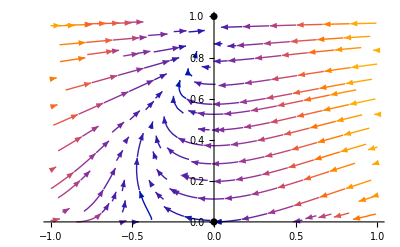

```mathematica
Show[FPsψvExpanding,PhaseSpaceψvExpanding]
```

```mathematica
uFlatSurface=Plot3D[{u},{ψ,-1,1},{v,0,1},PlotStyle->{{Darker[Green],Opacity[0.5]}},Mesh->None,AxesLabel->{"ψ","v","u"}]
```

-Graphics3D-

```mathematica
u=Sqrt[v/3+(ψ^2)/6]
```

√(v/3+ψ^2/6)

```mathematica
Clear[u]
```

```mathematica
deψ:=ψ'=-3*u*ψ-2*Sqrt[v]*(1-Sqrt[v])
dev:=v'=-2*ψ*Sqrt[v]*(1-Sqrt[v])
deu:=u'=-u^2-(1/3)*(ψ^2-v)
```

```mathematica
uPhaseSpace=StreamPlot3D[{deψ,dev,deu},{ψ,-1,1},{v,0,1},{u,0,1},AxesLabel->{"ψ","v","u"}]
```

Min::nord: Invalid comparison with -0.183751+2.634×10^-10 ⅈ attempted.

Max::nord: Invalid comparison with -0.183751+2.634×10^-10 ⅈ attempted.

Min::nord: Invalid comparison with -0.540569-6.25663×10^-10 ⅈ attempted.

Max::nord: Invalid comparison with -0.540569-6.25663×10^-10 ⅈ attempted.

Min::nord: Invalid comparison with -0.960914-2.96664×10^-9 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Max::nord: Invalid comparison with -0.960914-2.96664×10^-9 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[uFlatSurface,uPhaseSpace,PlotRange->All]
```

-Graphics3D-

## Dimensionless Variables - 2D - V-ψ phase space - Contracting

```mathematica
Clear[ψ];
```

```mathematica
u=-Sqrt[v/3+(ψ^2)/6]
```

-√(v/3+ψ^2/6)

```mathematica
deψ:=ψ'=-3*u*ψ-2*Sqrt[v]*(1-Sqrt[v])
dev:=v'=-2*ψ*Sqrt[v]*(1-Sqrt[v])
```

```mathematica
(*Solve the system of equations for the fixed points*)
FPs=Solve[{deψ==0,dev==0},{ψ,v}]
```

{{ψ→0,v→0},{ψ→0,v→1},{ψ→-ⅈ √2,v→1},{ψ→ⅈ √2,v→1}}

```mathematica
FindRoot[{deψ==0,dev==0},{ψ,1},{v,0.05}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{ψ→0.0100182+0.00282231 ⅈ,v→1.63777×10^-9+3.21799×10^-9 ⅈ}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={ψ/.FPs[[1,1]],v/.FPs[[1,2]]};
FP[2]={ψ/.FPs[[2,1]],v/.FPs[[2,2]]};
FP[3]={ψ/.FPs[[3,1]],v/.FPs[[3,2]]};
FP[4]={ψ/.FPs[[4,1]],v/.FPs[[4,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,4}];
```

```mathematica
FPsψvExpanding=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[deψ,ψ],D[deψ,v]},{D[dev,ψ],D[dev,v]}}];
J//MatrixForm
```

((√6 (v+ψ^2))/(√(2 v+ψ^2)) | 2-1/(√v)+(√(3/2) ψ)/(√(2 v+ψ^2))
2 (-√v+v) | (2-1/(√v)) ψ)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{ψ->FixedPoints[[i,1]],v->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{ψ->FixedPoints[[i,1]],v->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{ψ->FixedPoints[[i,1]],v->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,4}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √6 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 √(3/2) ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (Indeterminate | Indeterminate
0 | Indeterminate) | Eigenvalues[{{Indeterminate,Indeterminate},{0,Indeterminate}}] | Eigenvectors[{{Indeterminate,Indeterminate},{0,Indeterminate}}]
(0
1) | (√3 | 1
0 | 0) | (√3
0) | (1 | 0
-1/(√3) | 1)
(-ⅈ √2
1) | (ComplexInfinity | ComplexInfinity
0 | -ⅈ √2) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{0,-ⅈ √2}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{0,-ⅈ √2}}]
(ⅈ √2
1) | (ComplexInfinity | ComplexInfinity
0 | ⅈ √2) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{0,ⅈ √2}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{0,ⅈ √2}}]

```mathematica
PhaseSpaceψvExpanding=StreamPlot[{deψ,dev},{ψ,-1,1},{v,-1,1}];
```

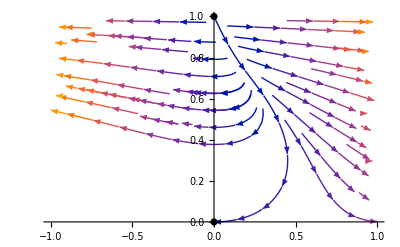

```mathematica
Show[FPsψvExpanding,PhaseSpaceψvExpanding]
```

## Dimensionless Variables - 2D - u-ψ Phase Space

```mathematica
v=3*u^2-(ψ^2)/2
```

3 u^2-ψ^2/2

```mathematica
deu:=u'=-u^2-(1/3)*(ψ^2-v)
deψ:=ψ'=-3*u*ψ-2*Sqrt[v]*(1-Sqrt[v])
```

```mathematica
(*Solve the system of equations for the fixed points*)
FPs=Solve[{deu==0,deψ==0},{u,ψ}]
```

{{u→0,ψ→0},{u→-1/(√3),ψ→0},{u→1/(√3),ψ→0}}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={u/.FPs[[1,1]],ψ/.FPs[[1,2]]};
FP[2]={u/.FPs[[2,1]],ψ/.FPs[[2,2]]};
FP[3]={u/.FPs[[3,1]],ψ/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,3}];
```

```mathematica
FPsuψ=ListPlot[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[deu,u],D[deu,ψ]}, {D[deψ,u],D[deψ,ψ]}}];
J//MatrixForm
```

(0 | -ψ
-3 ψ+u (12-6/(√(3 u^2-ψ^2/2))) | -3 u+ψ (-2+1/(√(3 u^2-ψ^2/2))))

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{u->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J/.{u->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{u->FixedPoints[[i,1]],ψ->FixedPoints[[i,2]]}]]//MatrixForm},{i,1,3}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (0 | 0
Indeterminate | Indeterminate) | Eigenvalues[{{0,0},{Indeterminate,Indeterminate}}] | Eigenvectors[{{0,0},{Indeterminate,Indeterminate}}]
(-1/(√3)
0) | (0 | 0
-2 √3 | √3) | (√3
0) | (0 | 1
1 | 2)
(1/(√3)
0) | (0 | 0
2 √3 | -√3) | (-√3
0) | (0 | 1
1 | 2)

```mathematica
PhaseSpaceuψ=StreamPlot[{deu,deψ},{u,-1,1},{ψ,-1,1}];
```

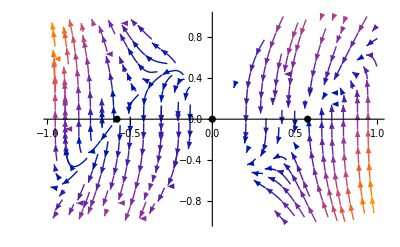

```mathematica
Show[FPsuψ,PhaseSpaceuψ,PlotRange->All]
```

```mathematica
v=3*u^2-(ψ^2)/2
```

3 u^2-ψ^2/2

```mathematica
deu:=u'=-u^2-(1/3)*(ψ^2-v)
deψ:=ψ'=-3*u*ψ-2*Sqrt[v]*(1-Sqrt[v])
dev:=v'=-2*ψ*Sqrt[v]*(1-Sqrt[v])
```

```mathematica
vPhaseSpace=StreamPlot3D[{deu,deψ,dev},{u,-1,1},{ψ,-1,1},{v,0,1}];
```

Min::nord: Invalid comparison with -0.434113-9.37038×10^-10 ⅈ attempted.

Max::nord: Invalid comparison with -0.434113-9.37038×10^-10 ⅈ attempted.

Min::nord: Invalid comparison with 0.340389-3.43263×10^-9 ⅈ attempted.

Max::nord: Invalid comparison with 0.340389-3.43263×10^-9 ⅈ attempted.

Min::nord: Invalid comparison with -0.340052+1.35685×10^-9 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Max::nord: Invalid comparison with -0.340052+1.35685×10^-9 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
vFlatSurface=Plot3D[v,{u,-1,1},{ψ,-1,1},PlotStyle->{Darker[Green],Opacity[0.5]},Mesh->None]
```

-Graphics3D-

```mathematica
Show[vPhaseSpace,vFlatSurface,AxesLabel->{"u","ψ","v"}]
```

-Graphics3D-

## H, ψ, V Variables

```mathematica
(3*H0^2-(ψ0^2)/2)
```

```mathematica
deVt:=V'[t]==-2*(3*H0^2-(ψ0^2)/2)*ψ[t]*Sqrt[V[t]/(3*H0^2-(ψ0^2)/2)]*(1-Sqrt[V[t]/(3*H0^2-(ψ0^2)/2)])
deψt:=ψ'[t]==-3*H[t]*ψ[t]-2*(3*H0^2-(ψ0^2)/2)*Sqrt[V[t]/(3*H0^2-(ψ0^2)/2)]*(1-Sqrt[V[t]/(3*H0^2-(ψ0^2)/2)])
deHt:=H'[t]==-H[t]^2-(1/6)*(2*ψ[t]^2-2*V[t])
```

```mathematica
Clear[V0]
```

```mathematica
N[Sqrt[1/3],3]
```

0.577

```mathematica
N[Sqrt[1+(0.5^2)/6],3]
```

1.02062

```mathematica
ψ0=0.5
```

0.5

```mathematica
traj[H0_,β_]=NDSolve[{deHt,deψt,deVt,H[0]==H0,ψ[0]==β*ψ0,V[0]==3*H0^2-(ψ0^2)/2},{H,ψ,V},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition H0 is not a number or a rectangular array of numbers.

NDSolve[{H'[t]==-H[t]^2+1/6 (2 V[t]-2 ψ[t]^2),ψ'[t]==-2 (-0.125+3 H0^2) √(V[t]/(-0.125+3 H0^2)) (1-√(V[t]/(-0.125+3 H0^2)))-3 H[t] ψ[t],V'[t]==-2 (-0.125+3 H0^2) √(V[t]/(-0.125+3 H0^2)) (1-√(V[t]/(-0.125+3 H0^2))) ψ[t],H[0]==H0,ψ[0]==0.5 β,V[0]==-0.125+3 H0^2},{H,ψ,V},{t,-100,100}]

```mathematica
sol[1]=traj[0.5,1]
```

NDSolve::ndsz: At t == -1.12793, step size is effectively zero; singularity or stiff system suspected.

{{H→InterpolatingFunction[…],ψ→InterpolatingFunction[…],V→InterpolatingFunction[…]}}

```mathematica
sol[2]=traj[-0.5,-1]
```

NDSolve::ndsz: At t == 1.12793, step size is effectively zero; singularity or stiff system suspected.

{{H→InterpolatingFunction[…],ψ→InterpolatingFunction[…],V→InterpolatingFunction[…]}}

```mathematica
sol[3]=traj[0.7,1]
```

NDSolve::ndsz: At t == -0.947627, step size is effectively zero; singularity or stiff system suspected.

{{H→InterpolatingFunction[…],ψ→InterpolatingFunction[…],V→InterpolatingFunction[…]}}

```mathematica
traj3D[1]=ParametricPlot3D[Evaluate[{{H[t],ψ[t],V[t]}}/.sol[1],{t,-1.12,100},PlotStyle -> {{Black}}],PlotRange->{{-1,1},{-1,1},{0,1}},PlotPoints->200];
```

```mathematica
traj3D[2]=ParametricPlot3D[Evaluate[{{H[t],ψ[t],V[t]}}/.sol[2],{t,-100,1.12},PlotStyle -> {{Black}}],PlotRange->{{-1,1},{-1,1},{0,1}},PlotPoints->200];
```

```mathematica
traj3D[3]=ParametricPlot3D[Evaluate[{{H[t],ψ[t],V[t]}}/.sol[3],{t,-0.947,100},PlotStyle -> {{Black}}],PlotRange->{{-1,1},{-1,1},{0,1}},PlotPoints->200];
```

```mathematica
trajectories=Table[traj3D[i],{i,1,3}];
```

```mathematica
FlatSurf=ContourPlot3D[H^2==V/3+ψ^2/6,{H,-1,1},{ψ,-1,1},{V,0,1},ContourStyle->{Darker[Green],Opacity[0.5]},Mesh->None];
```

```mathematica
Show[FlatSurf,trajectories]
```

-Graphics3D-

```mathematica
deV:=V'=-2*V0*ψ*Sqrt[V/V0]*(1-Sqrt[V/V0])
deψ:=ψ'=-3*H*ψ-2*V0*Sqrt[V/V0]*(1-Sqrt[V/V0])
deH:=H'=-H^2-(1/6)*(2*ψ^2-2*V)
```

```mathematica
V0=1
```

1

```mathematica
PhaseSpaceFull=StreamPlot3D[{deH,deψ,deV},{H,-1,1},{ψ,-1,1},{V,0,1}];
```

Min::nord: Invalid comparison with -0.434113-9.37038×10^-10 ⅈ attempted.

Max::nord: Invalid comparison with -0.434113-9.37038×10^-10 ⅈ attempted.

Min::nord: Invalid comparison with 0.340389-3.43263×10^-9 ⅈ attempted.

Max::nord: Invalid comparison with 0.340389-3.43263×10^-9 ⅈ attempted.

Min::nord: Invalid comparison with -0.340052+1.35685×10^-9 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Max::nord: Invalid comparison with -0.340052+1.35685×10^-9 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
Show[PhaseSpaceFull,FlatSurf]
```

-Graphics3D-

## Try 2

```mathematica
(*plot3d[u,Psi,v=v{u,psi)}]*)
```

```mathematica
deu:=u'=-u^2-(1/3)*(ψ^2-v)
deψ:=ψ'=-3*u*ψ-2*Sqrt[v]*(1-Sqrt[v])
dev:=v'=-2*ψ*Sqrt[v]*(1-Sqrt[v])
```

```mathematica
devt:=v'[t]==-2*ψ[t]*Sqrt[v[t]]*(1-Sqrt[v[t]])
deψt:=ψ'[t]==-3*u[t]*ψ[t]-2*Sqrt[v[t]]*(1-Sqrt[v[t]])
deut:=u'[t]==-u[t]^2-(1/6)*(2*ψ[t]^2-2*v[t])
```

```mathematica
Clear[V0]
```

```mathematica
N[Sqrt[1/3],3]
```

0.577

```mathematica
N[Sqrt[(2+0.5^2)/6]]
```

0.612372

```mathematica
N[0.5/Sqrt[6]]
```

0.204124

```mathematica
ψ0=0.5
```

0.5

```mathematica
traj[u0_,β_]=NDSolve[{deut,deψt,devt,u[0]==u0,ψ[0]==β*ψ0,v[0]==3*u0^2-(ψ0^2)/2},{u,ψ,v},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition u0 is not a number or a rectangular array of numbers.

NDSolve[{u'[t]==-u[t]^2+1/6 (2 v[t]-2 ψ[t]^2),ψ'[t]==-2 (1-√v[t]) √v[t]-3 u[t] ψ[t],v'[t]==-2 (1-√v[t]) √v[t] ψ[t],u[0]==u0,ψ[0]==0.5 β,v[0]==-0.125+3 u0^2},{u,ψ,v},{t,-100,100}]

```mathematica
sol[1]=traj[0.5,1]
```

NDSolve::ndsz: At t == -1.04838, step size is effectively zero; singularity or stiff system suspected.

{{u→InterpolatingFunction[…],ψ→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

```mathematica
sol[2]=traj[-0.5,-1]
```

NDSolve::ndsz: At t == 1.04838, step size is effectively zero; singularity or stiff system suspected.

{{u→InterpolatingFunction[…],ψ→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

```mathematica
sol[3]=traj[0.4,1]
```

NDSolve::ndsz: At t == -1.10848, step size is effectively zero; singularity or stiff system suspected.

{{u→InterpolatingFunction[…],ψ→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

```mathematica
traj3D[1]=ParametricPlot3D[Evaluate[{{u[t],ψ[t],v[t]}}/.sol[1],{t,-1.04,100},PlotStyle -> {{Black}}],PlotRange->{{-1,1},{-1,1},{0,1}},PlotPoints->500];
```

```mathematica
traj3D[2]=ParametricPlot3D[Evaluate[{{u[t],ψ[t],v[t]}}/.sol[2],{t,-100,1.04},PlotStyle -> {{Black}}],PlotRange->{{-1,1},{-1,1},{0,1}},PlotPoints->500];
```

```mathematica
traj3D[3]=ParametricPlot3D[Evaluate[{{u[t],ψ[t],v[t]}}/.sol[3],{t,-1.1,100},PlotStyle -> {{Black}}],PlotRange->{{-1,1},{-1,1},{0,1}},PlotPoints->500];
```

```mathematica
trajectories=Table[traj3D[i],{i,1,3}];
```

```mathematica
FlatSurf=ContourPlot3D[u^2==v/3+ψ^2/6,{u,-1,1},{ψ,-1,1},{v,0,1},ContourStyle->{Darker[Green],Opacity[0.5]},Mesh->None];
```

```mathematica
Show[FlatSurf,trajectories]
```

-Graphics3D-

## Compactification

```mathematica
deV:=V'=-2*(Ψ/Sqrt[1-Ψ^2])*Sqrt[V]*(1-Sqrt[V])
deU:=U'=-U^2*Sqrt[1-U^2]-(((1-U^2)^(3/2))/3)*(Ψ^2/(1-Ψ^2)-V)
deΨ:=Ψ'=-3*U*Ψ*(1-Ψ^2)/Sqrt[1-U^2]-2*(1-Ψ^2)^(3/2)*Sqrt[V]*(1-Sqrt[V])
```

```mathematica
(*Solve the system of equations for the fixed points*)
FPs=Solve[{deU==0,deΨ==0,deV==0},{U,Ψ,V}]
```

{{u→0,ψ→0,v→0},{u→0,ψ→0,v→0},{u→-1/(√3),ψ→0,v→1},{u→1/(√3),ψ→0,v→1},{u→0,ψ→-1,v→1},{u→-1/(√3),ψ→0,v→1},{u→1/(√3),ψ→0,v→1},{u→0,ψ→1,v→1}}

```mathematica
(*Remove arrows from the fixed points and put them into a common variable name*)
FP[1]={U/.FPs[[1,1]],Ψ/.FPs[[1,2]],V/.FPs[[1,3]]};
FP[2]={U/.FPs[[3,1]],Ψ/.FPs[[3,2]],V/.FPs[[3,3]]};
FP[3]={U/.FPs[[4,1]],Ψ/.FPs[[4,2]],V/.FPs[[4,3]]};
FP[4]={U/.FPs[[5,1]],Ψ/.FPs[[5,2]],V/.FPs[[5,3]]};
FP[5]={U/.FPs[[8,1]],Ψ/.FPs[[8,2]],V/.FPs[[8,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FixedPoints=Table[FP[i],{i,1,5}];
```

```mathematica
FixedPointsPlot=ListPointPlot3D[FixedPoints,PlotStyle->Black];
```

```mathematica
(*Find the general Jacobian*)
J=Simplify[{{D[deU,U],D[deU,Ψ],D[deU,V]}, {D[deΨ,U],D[deΨ,Ψ],D[deΨ,V]},{D[deV,U],D[deV,Ψ],D[deV,V]}}];
J//MatrixForm
```

(-2 u | -(2 ψ)/3 | 1/3
-3 ψ | -3 u | 2-1/(√v)
0 | 2 (-√v+v) | (2-1/(√v)) ψ)

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each fixed point*)
FPTable=Table[{FixedPoints[[i]]//MatrixForm,Simplify[J/.{U->FixedPoints[[i,1]],Ψ->FixedPoints[[i,2]],V->FixedPoints[[i,3]]}]//MatrixForm,Simplify[Eigenvalues[J/.{U->FixedPoints[[i,1]],Ψ->FixedPoints[[i,2]],V->FixedPoints[[i,3]]}]]//MatrixForm,Simplify[Eigenvectors[J/.{U->FixedPoints[[i,1]],Ψ->FixedPoints[[i,2]],V->FixedPoints[[i,3]]}]]//MatrixForm},{i,1,5}];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvectors::inf: Input matrix contains an infinite entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix, eigenvalues and eigenvectors*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0
0) | (0 | 0 | 1/3
0 | 0 | ComplexInfinity
0 | 0 | Indeterminate) | Eigenvalues[{{0,0,1/3},{0,0,ComplexInfinity},{0,0,Indeterminate}}] | Eigenvectors[{{0,0,1/3},{0,0,ComplexInfinity},{0,0,Indeterminate}}]
(-1/(√3)
0
1) | (2/(√3) | 0 | 1/3
0 | √3 | 1
0 | 0 | 0) | (√3
2/(√3)
0) | (0 | 1 | 0
1 | 0 | 0
-1/(2 √3) | -1/(√3) | 1)
(1/(√3)
0
1) | (-2/(√3) | 0 | 1/3
0 | -√3 | 1
0 | 0 | 0) | (-√3
-2/(√3)
0) | (0 | 1 | 0
1 | 0 | 0
1/(2 √3) | 1/(√3) | 1)
(0
-1
1) | (0 | 2/3 | 1/3
3 | 0 | 1
0 | 0 | -1) | (-√2
√2
-1) | (-(√2)/3 | 1 | 0
(√2)/3 | 1 | 0
-1/3 | 0 | 1)
(0
1
1) | (0 | -2/3 | 1/3
-3 | 0 | 1
0 | 0 | 1) | (-√2
√2
1) | ((√2)/3 | 1 | 0
-(√2)/3 | 1 | 0
1/3 | 0 | 1)

```mathematica
CompactFlatSurface=ContourPlot3D[U^2/(1-U^2)==v/3+Ψ^2/(1-Ψ^2),{U,-1,1},{Ψ,-1,1},{v,0,1},ContourStyle->{Darker[Green],Opacity[0.5]},Mesh->None]
```

-Graphics3D-

```mathematica
deVt:=V'[t]==-2*(Ψ[t]/Sqrt[1-Ψ[t]^2])*Sqrt[V[t]]*(1-Sqrt[V[t]])
deUt:=U'[t]==-U[t]^2*Sqrt[1-U[t]^2]-(((1-U[t]^2)^(3/2))/3)*(Ψ[t]^2/(1-Ψ[t]^2)-V[t])
deΨt:=Ψ'[t]==-3*U[t]*Ψ[t]*(1-Ψ[t]^2)/Sqrt[1-U[t]^2]-2*(1-Ψ[t]^2)^(3/2)*Sqrt[V[t]]*(1-Sqrt[V[t]])
```

```mathematica
traj1[U0_,Ψ0_,V0_]=NDSolve[{deUt,deΨt,deVt,U[0]==U0,Ψ[0]==Ψ0,V[0]==V0},{U,Ψ,V},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition U0 is not a number or a rectangular array of numbers.

NDSolve[{U'[t]==-U[t]^2 √(1-U[t]^2)-1/3 (1-U[t]^2)^(3/2) (-V[t]+Ψ[t]^2/(1-Ψ[t]^2)),Ψ'[t]==-(3 U[t] Ψ[t] (1-Ψ[t]^2))/(√(1-U[t]^2))-2 (1-√V[t]) √V[t] (1-Ψ[t]^2)^(3/2),V'[t]==-(2 (1-√V[t]) √V[t] Ψ[t])/(√(1-Ψ[t]^2)),U[0]==U0,Ψ[0]==Ψ0,V[0]==V0},{U,Ψ,V},{t,-100,100}]

```mathematica
sol[1]=traj1[.5,.2,.5]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,ComplexInfinity,Indeterminate} is not a list of numbers with dimensions {3} at {t,U[t],V[t],Ψ[t]} = {-1.1497,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}.

{{U→InterpolatingFunction[…],Ψ→InterpolatingFunction[…],V→InterpolatingFunction[…]}}

```mathematica
sol[2]=traj1[-.5,-.1,.5]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

NDSolve::nlnum: The function value {ComplexInfinity,ComplexInfinity,0.+0. ⅈ} is not a list of numbers with dimensions {3} at {t,U[t],V[t],Ψ[t]} = {1.26289,-1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ}.

{{U→InterpolatingFunction[…],Ψ→InterpolatingFunction[…],V→InterpolatingFunction[…]}}

```mathematica
sol[3]=traj1[.8,.1,.5]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

NDSolve::nlnum: The function value {ComplexInfinity,ComplexInfinity,0.+0. ⅈ} is not a list of numbers with dimensions {3} at {t,U[t],V[t],Ψ[t]} = {-0.619552,1.+0. ⅈ,0.999999+0. ⅈ,1.+0. ⅈ}.

{{U→InterpolatingFunction[…],Ψ→InterpolatingFunction[…],V→InterpolatingFunction[…]}}

```mathematica
sol[4]=traj1[-.9,-.1,.5]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,ComplexInfinity,Indeterminate} is not a list of numbers with dimensions {3} at {t,U[t],V[t],Ψ[t]} = {0.418657,-1.+0. ⅈ,0.999999+0. ⅈ,-1.+0. ⅈ}.

{{U→InterpolatingFunction[…],Ψ→InterpolatingFunction[…],V→InterpolatingFunction[…]}}

```mathematica
sol[5]=traj1[-.1,-.1,.5]
```

{{U→InterpolatingFunction[…],Ψ→InterpolatingFunction[…],V→InterpolatingFunction[…]}}

```mathematica
sol[6]=traj1[.1,.1,.5]
```

{{U→InterpolatingFunction[…],Ψ→InterpolatingFunction[…],V→InterpolatingFunction[…]}}

```mathematica
sol[7]=traj1[.1,.1,0.999]
```

{{U→InterpolatingFunction[…],Ψ→InterpolatingFunction[…],V→InterpolatingFunction[…]}}

```mathematica
sol[8]=traj1[.1,.1,.1]
```

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

NDSolve::nlnum: The function value {0.+0. ⅈ,2.779+0. ⅈ,ComplexInfinity} is not a list of numbers with dimensions {3} at {t,U[t],V[t],Ψ[t]} = {-2.49527,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}.

{{U→InterpolatingFunction[…],Ψ→InterpolatingFunction[…],V→InterpolatingFunction[…]}}

```mathematica
traj3D[1]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[1],{t,-1.14,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[2]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[2],{t,-100,1.25},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}},AxesLabel->{"u","ψ","v"}];
```

```mathematica
traj3D[3]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[3],{t,-0.61,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[4]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[4],{t,-100,0.418},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[5]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}},AxesLabel->{"u","ψ","v"}];
```

```mathematica
traj3D[6]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[6],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[7]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[7],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}}];
```

```mathematica
traj3D[8]=ParametricPlot3D[Evaluate[{{u1[t],ψ1[t],v1[t]}}/.sol[8],{t,-2.49,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-1,1},{-1,1},{0,1}},PlotPoints->200];
```

```mathematica
trajectories=Table[traj3D[i],{i,1,8}];
```

```mathematica
Show[CompactFlatSurface,trajectories,AxesLabel->{"u","ψ","v"}]
```

-Graphics3D-